```mathematica
Clear["all"]
```

We take Ω as the reference frequency and set its numerical value to 1 (ℏΩ will be the fundamental unit of energy  of the system)

In order to guarantee that the detector has enough resolution to “see” // “capture” the interference peaks without the relaxation 
thicken the main peaks of the spectrum we fixed the ratio Ω / Γ to 4. Thus we set Γ = 0.25. 

Since the probability of a non-adiabatic transition is dictated by the ratio Ω / β   through   exp ( - π Ω^2 / 2 β^2 )  and we have fixed the value of Ω, the only parameter that governs the dynamical behavior of the qubit-laser coupling is the value of β^2. 

We want to analyze how the characteristics of the ideal stationary fluorescence spectrum of the system change as we pass from a completely adiabatic limit  β ≪1 to β ∼1.

Adiabatic limit: 
β = 0.3  so β^2 = 0.09  and P_LZ≈2×10^-8

In this case the emission will follow one of the adiabatic hyperbolic branches of the avoided crossing . There will not be  transient (ringing) oscillations since there will not be any coherence superposition of paths. 

Non-adiabatic regime:
β  = 0.5 so β^2 = 0.25  and P_LZ≈0.08

Time scale: Instead of plotting the spectrum against time $t$, spectrum should be plot it against the instantaneous dimensionless detuning:
τ==(Δ(t))/Ω==(β^2 t)/Ω

Since we already fixed Ω to 1 we only need to change the time axis t by the axis β^2t. 

In this way we don’t need to use different time scales to “see” the transition for different values of the rate β^2. Otherwise the avoided crossings will appear distorted (some very stretched, others very squashed), ruining the direct comparison.

In this way the adiabatic lines of the avoided crossing , the X shape, will have the same step and the same geometric aperture for different rates of change β^2. This will allow the reader to see different density maps side by side and observe exclusively how the intensity of light decides which path to take in the face of the same band structure.

Frequency scale and axis: 

ω_max≈(±β)^2 t_max

ω_borde==β^2 t_max+Margin

Margin = 2Ω

Avoided Crossing: 

Diabatic lines (non-coupled states) : ω_diab(t)==±Δ(t)==± β^2t
Adiabatic lines (coupled states, instantaneous energy eigenvalues):   ω_adiab(t)==±√(Δ(t)^2+Ω^2)==±√((β^2 t)^2+Ω^2)

```mathematica
ClearAll["Global`*"]
```

```mathematica
β=0.25;
Ω=1.0;
Γ = 0.25  ;

Δ[t_]:=(β^2 )t;
Δdot:=β^2;

t0 = -10* (Ω/β^2); 
tf = 10*(Ω/β^2);
```

## Evaluation of the system of equations V2

The system of equations for the alpha functions can be algebraically resolved into three equations. Basically, all the dynamic information of the problem is encoded in the first Riccati equation.  

Instead of solving this non-linear 1st order ODE

```mathematica
eqPlus={αp'[t]==-I(Δ[t] αp[t] - Ω/2(αp[t]^2 - 1)),αp[t0]==0};
alphaMas=NDSolveValue[eqPlus,αp,{t,t0,tf},Method->{"StiffnessSwitching"}, AccuracyGoal->10, PrecisionGoal->10];
```

we apply the usual change of variable:        α_+(t) = - 1/(c(t))(u'(t))/(u(t)),   to transform the equation into a 2nd order ODE for u(t)

```mathematica
eqU={u''[t]+I Δ[t] u'[t]+Ω^2/4 u[t]==0,u[t0]==1,u'[t0]==0};
uSol=NDSolveValue[eqU,u,{t,t0,tf},Method->{"StiffnessSwitching"}];
alphaMas2[t_]:=(2 I/Ω)uSol'[t]/uSol[t];
```

More over, we can apply a second change of variable to eliminate de 1st order derivate of the previous equation:   u(t)=exp[−  i/2​∫ Δ(s)ds ] v(t),

The resulting equation for v(t) is  :     v’’(t) + (Ω^2/4 +  Δ^2/4- i/2Δ’  ) v(t) = 0
with initial conditions:      v(t0​)=1    ,    v’(t0) = i/2Δ(t0)

And the reconstruction of α_+ follows as :   α_+ = Δ[t]/Ω +((2 I)/Ω) v'[t]/v[t];

```mathematica
eqV = {v''[t] + (Ω^2/4+ Δ[t]^2/4- I Δdot/2)v[t] == 0, v[t0]== 1, v'[t0]== I/2 Δ[t0]};
vSol=NDSolveValue[eqV,v,{t,t0,tf},Method->{"StiffnessSwitching"}];
alphaMas[t_]:= Δ[t]/Ω +((2 I)/Ω) (vSol'[t]/vSol[t]);
```

Now we use the result for α_+ to evaluate the remaining equations

```mathematica
eqZ={αz'[t]==(I/2) (Ω*alphaMas[t]-Δ[t]),αz[t0]==0};
alphaZ=NDSolveValue[eqZ,αz,{t,t0,tf},Method->{"StiffnessSwitching"}, AccuracyGoal->10, PrecisionGoal->10];
```

```mathematica
eqMinus={αm'[t]==-(I Ω/2 )Exp[2 alphaZ[t]], αm[t0]==0};
alphaMin=NDSolveValue[eqMinus,αm,{t,t0,tf},Method->{"StiffnessSwitching"}, AccuracyGoal->10, PrecisionGoal->10];
```

Test the result

```mathematica
Head[alphaMas]
```

Symbol

```mathematica
alphaMas[0]
```

0.981128+0.034096 ⅈ

```mathematica
alphaMas2[0]
```

0.981098+0.0340847 ⅈ

```mathematica
alphaMas3[0]
```

0.981171+0.0347678 ⅈ

Evolution Operator

```mathematica
U[t_]:={{Exp[alphaZ[t]]+Exp[-alphaZ[t]] alphaMin[t] alphaMas[t],Exp[-alphaZ[t]] alphaMas[t]},{Exp[-alphaZ[t]] alphaMin[t],Exp[-alphaZ[t]]}};
```

### Integrals as ODEs

```mathematica
SpectrumIntegrals[ω_?NumericQ,Γ_?NumericQ]:=
Module[
{I1,I2},
I1=NDSolveValue[{y1'[t]==Exp[(Γ-I ω)t] Exp[-2 alphaZ[t]] alphaMin[t]^2,y1[t0]==0},y1,{t,t0,tf}];
I2=NDSolveValue[{y2'[t]==Exp[(Γ-I ω)t] Exp[-2 alphaZ[t]] alphaMin[t],y2[t0]==0},y2,{t,t0,tf}];
{I1,I2}
]
```

```mathematica
Spectrum[ω_,Γ_][t_]:=Module[
{I1,I2},{I1,I2}=SpectrumIntegrals[ω,Γ];
2 Γ Exp[-2 Γ t] (Abs[I1[t]]^2+Abs[I2[t]]^2)
]
```

```mathematica
g1=Function[t,Exp[-2 alphaZ[t]] alphaMin[t]^2];
g2=Function[t,Exp[-2 alphaZ[t]] alphaMin[t]];
```

```mathematica
specSolver=ParametricNDSolveValue[
Evaluate[{
y1'[t]==Exp[(Γ-I ω) t] g1[t],
y2'[t]==Exp[(Γ-I ω) t] g2[t],
y1[t0]==0,y2[t0]==0
}],
{y1,y2},
{t,t0,tf},
{ω},
Method->{"StiffnessSwitching"},
AccuracyGoal->12,
PrecisionGoal->12,
MaxSteps->Infinity
];
```

```mathematica
BuildSpectrum[ω_?NumericQ]:=Module[
{I1,I2},{I1,I2}=specSolver[ω];
Function[t,2 Γ Exp[-2 Γ t] (Abs[I1[t]]^2+Abs[I2[t]]^2)]
]
```

```mathematica
S=BuildSpectrum[0];
S
```

Function[t$,2 Γ Exp[-2 Γ t$] (Abs[I1$36443[t$]]^2+Abs[I2$36443[t$]]^2)]

```mathematica
S[-100]
```

0.031608

```mathematica
S[100]
```

10.6805

## Evaluation of the system of equations V1

```mathematica
Clear[alphaMas,alphaZ, alphaMin];
```

```mathematica
ecuacionesOptimizadas={x'[t]==-I(Δ[t] x[t] - Ω/2(x[t]^2 - 1)),y'[t]==(I/2)*(Ω*x[t]-(β^2)*t),z'[t]==-(I*Ω/2)*Exp[2*y[t]],x[t0]==0,y[t0]==0,z[t0]==0};
```

```mathematica
{alphaMas, alphaZ, alphaMin}=NDSolveValue[ecuacionesOptimizadas,{x,y, z},{t,t0, tf},AccuracyGoal->10, PrecisionGoal->10];
```

```mathematica
g1=Function[t,Exp[-2 alphaZ[t]] alphaMin[t]^2];
g2=Function[t,Exp[-2 alphaZ[t]] alphaMin[t]];

f1[t_?NumericQ,ω_?NumericQ]:=Exp[(Γ-I ω)t] g1[t];
f2[t_?NumericQ,ω_?NumericQ]:=Exp[(Γ-I ω)t] g2[t];
```

```mathematica
I1[Γ_?NumericQ, ω_?NumericQ, T_?NumericQ, T0_?NumericQ]:= 
Abs[NIntegrate[Exp[(Γ-I ω)t]g1[t],{t,T0 , T},  MaxRecursion->20, Method->"LevinRule"]]^2  (*Method->{"LevinRule"}*)

I2[Γ_?NumericQ, ω_?NumericQ, T_?NumericQ, T0_?NumericQ]:= 
Abs[NIntegrate[Exp[(Γ-I ω)t]g2[t],{t,T0,T},  MaxRecursion->20,Method->"LevinRule"]]^2   (*Method->{"GlobalAdaptive"}*)

SpectrumEW[Γ_?NumericQ,ω_?NumericQ,T_?NumericQ, T0_?NumericQ]:=2Γ Exp[-2Γ T](I1[Γ, ω,T, T0]+I2[Γ, ω,T,T0])
```

```mathematica
I1[Γ_?NumericQ, ω_?NumericQ, T_?NumericQ, T0_?NumericQ]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMin[t]^2, {t,T0 , T}, MaxRecursion->20, Method->"LevinRule"]]^2

I2[Γ_?NumericQ, ω_?NumericQ, T_?NumericQ, T0_?NumericQ]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2alphaZ[t]]alphaMin[t],{t,T0,T}, MaxRecursion->20, Method->"LevinRule"]]^2

SpectrumEW[Γ_?NumericQ,ω_?NumericQ,T_?NumericQ, T0_?NumericQ]:=2Γ Exp[-2Γ T](I1[Γ, ω,T, T0]+I2[Γ, ω,T,T0])
```

```mathematica
tiempos={-80,-56,-40,-24,-20,-16,-12,-8,-6,-4,-2,0,2,4,6,8,12,16,20,24,32,40,48,56};
```

```mathematica
tiempos={8,12,16,20,24,32,40,48,56};
```

```mathematica
step = 0.075;
step = 0.095;
tMin=Min[tiempos];
tMax=Max[tiempos];

ωmin =( β^2)*(tMin)-2.5*Ω; ωmax = ( β^2)*(tMax)+2.5*Ω;
```

```mathematica
datos3D=ParallelTable[Table[{ω,t,SpectrumEW[Γ,ω,t,t0]},{ω,ωmin,ωmax,step}],{t,tiempos}];
```

```mathematica
datos3DNuevos=ParallelTable[Table[
(*Mantenemos S evaluado en't',pero guardamos la coordenada Y como'beta^2*t'*)
{ω,β^2*t,SpectrumEW[Γ,ω,t,t0]},{ω,ωmin,ωmax,step}],{t,tiempos}];
```

```mathematica
(*Definimos una paleta de 11 colores basada en un degradado*)
paletaTiempo=Table[Blend[{RGBColor[0.1,0.2,0.6],RGBColor[0.5,0.1,0.5],RGBColor[0.8,0.2,0.2]},i/10],{i,0,21}];
(*paletaTiempo=Table[Blend[{RGBColor[0.1,0.2,0.6],RGBColor[0.5,0.1,0.5],RGBColor[0.8,0.2,0.2]},i/10],{i,0,10}];*)
paletaMagma=Table[Blend[{Black,Purple,RGBColor[0.8,0.2,0.2],Orange},i/10],{i,0,10}];
paletaOceano=Table[Blend[{RGBColor[0.1,0.1,0.4],RGBColor[0.2,0.6,0.6],RGBColor[0.9,0.8,0.2]},i/10],{i,0,10}];
paletaSunset=Table[ColorData["SunsetColors"][i/10],{i,0,10}];
paletaMonocromatica=Table[Blend[{RGBColor[0.05,0.1,0.25],RGBColor[0.6,0.7,0.85]},i/10],{i,0,10}];
```

```mathematica
(*Altura de la base para el sombreado*)
zBase=0;

(*Generamos automáticamente los Ticks del eje Y asociando cada índice entero con la cadena de texto de su tiempo real correspondiente*)
ticksY=Table[{i,Style[ToString[tiempos[[i]]],12]},{i,1,Length[tiempos]}];

grafico3DSombreadoEquispaciado=Style[Show[Graphics3D[Table[Module[{puntosOriginales,puntos,ptInicial,ptFinal,puntosPoligono,colorTraza},
(*1. Extraemos la lista de puntos {v,t,S} original*)
puntosOriginales=datos3D[[i]];
(*2. Mapeamos la lista sustituyendo la coordenada y (tiempo real) por el índice entero'i'.Cada punto pasa de {v,t,S} a {v,i,S}*)
puntos=Map[{#[[1]],i,#[[3]]}&,puntosOriginales];
(*3. Identificamos los extremos en la nueva escala indexada*)
ptInicial=puntos[[1]];
ptFinal=puntos[[-1]];
(*4. Cerramos la curva para el polígono usando el índice'i' fijo para el eje y*)
puntosPoligono=Join[puntos,{{ptFinal[[1]],i,zBase},{ptInicial[[1]],i,zBase}}];
(*5. Definimos el color gradiente continuo*)
colorTraza=ColorData["SunsetColors"][i/Length[datos3D]];
{
(*EL ÁREA SOMBREADA*)
EdgeForm[None],FaceForm[Directive[colorTraza,Opacity[0.4]]],Polygon[puntosPoligono],
(*LA CURVA SUPERIOR (TRAZA)*)
Darker[colorTraza,0.4],AbsoluteThickness[1.5],Line[puntos]
}
],
(*Recorremos todas las trazas de datos3D*)
{i,1,Length[datos3D]}]
],
(*---CONFIGURACIÓN DE EJES Y ESTÉTICA---*)
Axes->{True, True, False},
(*El rango de Y ahora va estrictamente desde 1 hasta el número total de trazas*)
PlotRange->{All,{1,Length[datos3D]}, {-0.2,9.2}},
(*Mantenemos tus ejes estáticos fijos:X enfrente,Y a la derecha,Z atrás*)
AxesEdge->{{-1,-1},{1,-1},{-1,1}},BoxRatios->{1,1.5,0.6},Boxed->False,
(*Inyectamos los Ticks personalizados en el eje Y para engañar al ojo humano*)
Ticks->{Automatic,ticksY,Automatic},BaseStyle->{FontFamily->"Times New Roman",FontSize->12,Black},
TicksStyle->Directive[FontSize->12,Black],Lighting->"Neutral",
AxesLabel->{Style["ω",FontSize->16,Italic],Style["t",FontSize->16,Italic],Style["S",FontSize->16,Italic]},
ImageSize->500,Antialiasing->True,
ViewProjection->"Orthographic"]]
```

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
(*1. Definimos un umbral mínimo para evitar el error de Log10[0].Un valor de 10^-6 o 10^-8 suele ser ideal.*)
epsilon=10^-6;
```

```mathematica
(*Transformamos la lista de trazas en una única lista continua de coordenadas*)
datosCompletos=Flatten[datos3D,1];
```

```mathematica
(*2. Transformamos la lista plana.A la coordenada z (Amplitud S) le aplicamos el Logaritmo en base 10*)
datosCompletosLog=Map[{#[[1]],#[[2]],Log10[#[[3]]+epsilon]}&,datosCompletos];
```

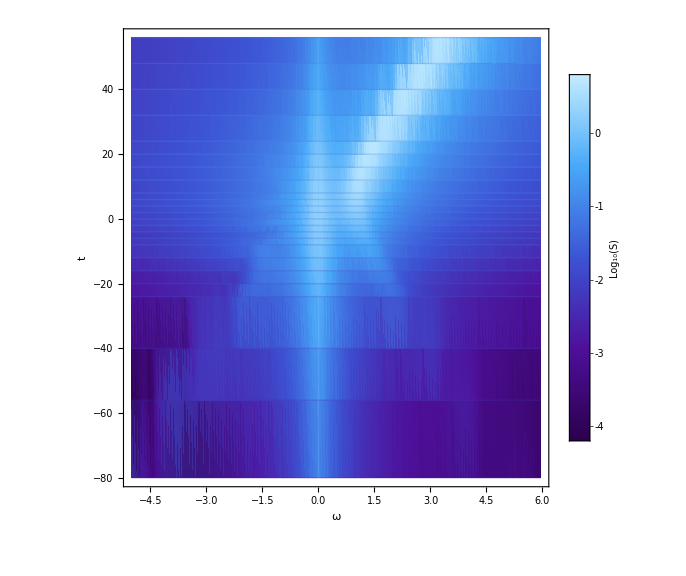

-Graphics-

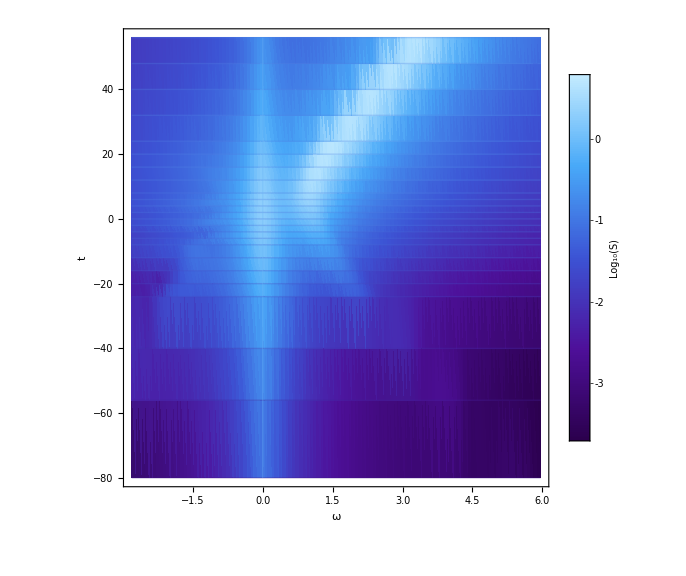

```mathematica
(*3. Generamos el Gráfico de Densidad con los nuevos datos*)
graficoDensidadLog=ListDensityPlot[datosCompletosLog,
(*---MALLA Y COLOR---*)
Mesh->{{0},tiempos},MeshStyle->Directive[Opacity[0.3],GrayLevel[0.1]],ColorFunction->"DeepSeaColors",

(*---CONFIGURACIÓN DE EJES Y ESTÉTICA---*)
PlotLegends->BarLegend[Automatic,LegendLabel->Style["\!\(\*SubscriptBox[\(Log\), \(10\)]\)(S)",14,Italic]],
Frame->True,FrameLabel->{Style["ω",16,Italic],Style["t",16,Italic]},
BaseStyle->{FontFamily->"Times New Roman",FontSize->12,Black},
TicksStyle->Directive[FontSize->12,Black],
(*Forzamos a que el renderizado muestre todo el rango logarítmico*)
PlotRange->All,
ImageSize->Large]
```

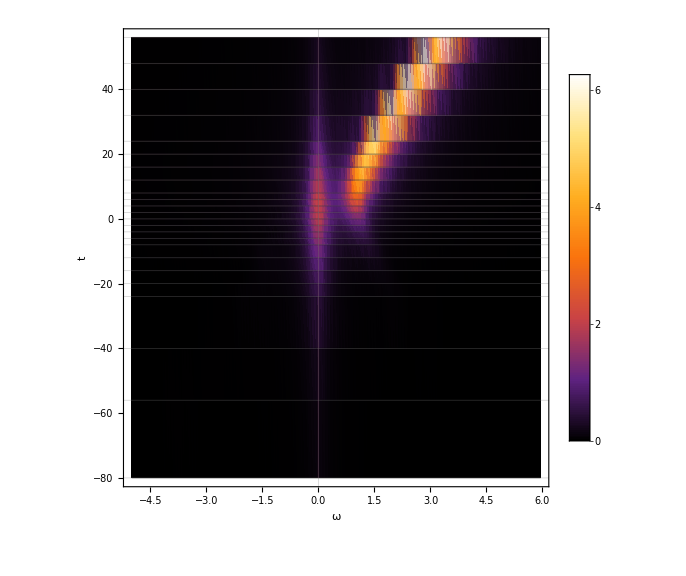

-Graphics-

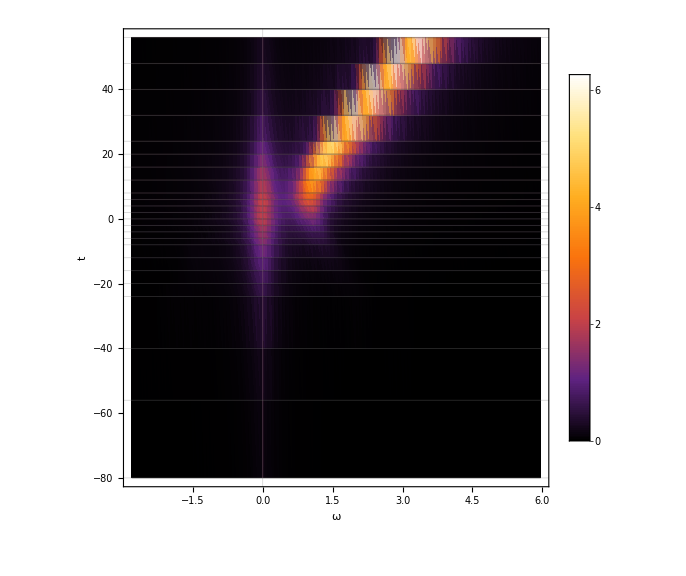

```mathematica
graficoDensidad2D=ListDensityPlot[datosCompletos,
(*---MALLA Y COLOR---*)
(*Forzamos una línea de malla sobre cada instante de tiempo real simluado*)
Mesh->{{0},tiempos},MeshStyle->Directive[Opacity[0.3],GrayLevel[0.1]],
ColorFunction->"SunsetColors",
(*---CONFIGURACIÓN DE EJES Y ESTÉTICA PROFESIONAL---*)
PlotLegends->Automatic,Frame->True,
FrameLabel->{Style["ω",16,Italic],Style["t",16,Italic]},
BaseStyle->{FontFamily->"Times New Roman",FontSize->12,Black},
TicksStyle->Directive[FontSize->12,Black],GridLines->{{0},tiempos},
PlotRange->All,ImageSize->Large]
```

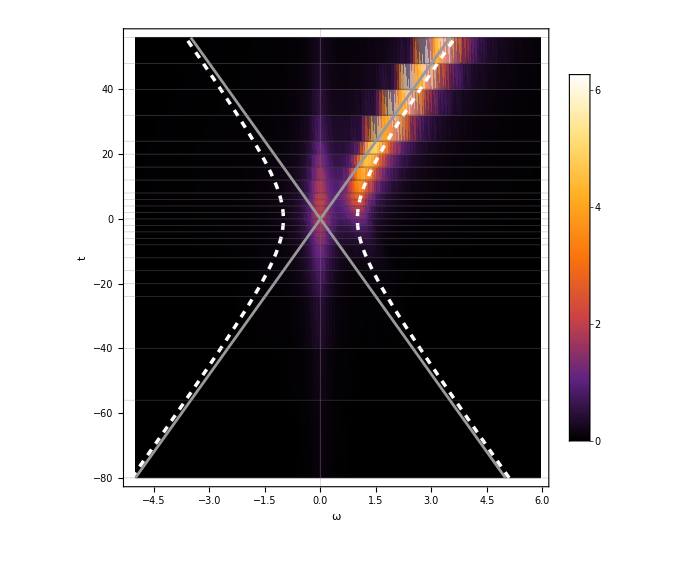

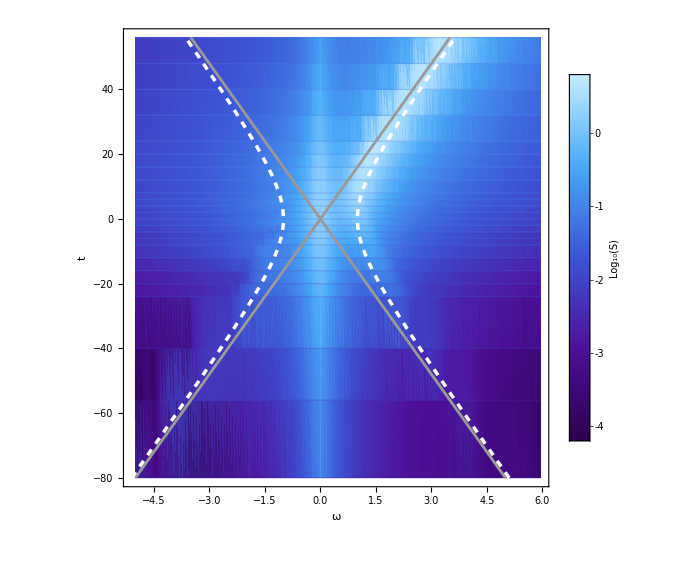

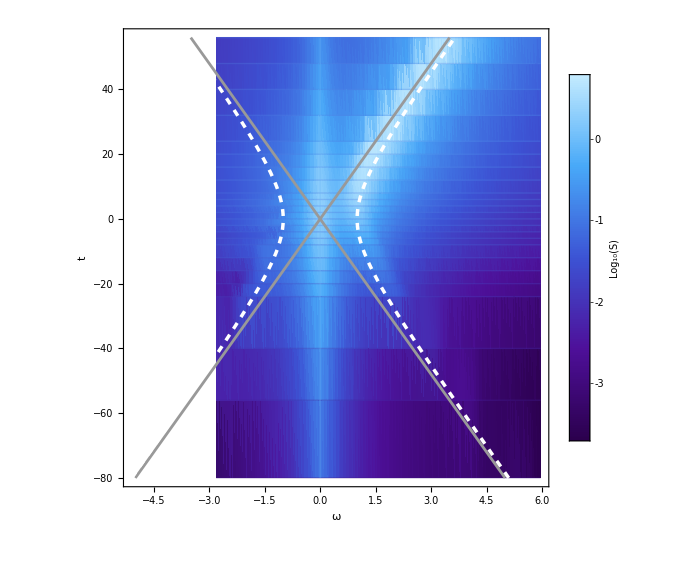

```mathematica
curvasTeoricas=ParametricPlot[{
(*Rama Diabática+(Derecha) e Izquierda*)
{β^2*t,t},{-β^2*t,t},
(*Rama Adiabática+(Derecha) e Izquierda*)
{Sqrt[(β^2*t)^2+Ω^2],t},{-Sqrt[(β^2*t)^2+Ω^2],t}},{t,tMin,tMax},

(*---CONFIGURACIÓN DE ESTILOS---*)
PlotStyle->{Directive[GrayLevel[0.6],AbsoluteThickness[2]],
(*Diabática+*)
Directive[GrayLevel[0.6],AbsoluteThickness[2]],
(*Diabática-*)
Directive[White,Dashed,AbsoluteThickness[2.5]],
(*Adiabática+*)
Directive[White,Dashed,AbsoluteThickness[2.5]]          
(*Adiabática-*)},
(*Quitamos los ejes propios del ParametricPlot para que no interfieran con el mapa*)
Axes->False,PlotRange->All];

(*4. Superponemos todo en una sola imagen*)
graficoFinalSuperpuesto=Show[
graficoDensidad2D,curvasTeoricas,
(*Forzamos a que el renderizado respete los límites de la simulación*)
PlotRange->All,
ImageSize->Large]
```

```mathematica
curvasTeoricas=ParametricPlot[{
(*Rama Diabática:{frecuencia,desintonía}*)
{β^2*t,β^2*t},{-β^2*t,β^2*t},
(*Rama Adiabática:{frecuencia,desintonía}*)
{Sqrt[(β^2*t)^2+Ω^2],β^2*t},{-Sqrt[(β^2*t)^2+Ω^2],β^2*t}},{t,tMin,tMax},PlotStyle->{Directive[GrayLevel[0.6],AbsoluteThickness[2]],Directive[GrayLevel[0.6],AbsoluteThickness[2]],Directive[White,Dashed,AbsoluteThickness[2.5]],Directive[White,Dashed,AbsoluteThickness[2.5]]},Axes->False,PlotRange->All];
```